```mathematica
Nt = 551; (*1000 -> default*)(*10 -> simple case to compare to reduced points*)
ti = 0; tf = 1; 
deltat = (tf - ti) /Nt ;
Nx = 551; (*500 default from problem*)(*200 -> my choice*) (*25 -> simple case to compare to reduced points*)
xi = 0; xf = 2*Pi; 
deltax = (xf - xi) / Nx; 
c =  1;
r = c * (deltat / deltax);

(*For Eigenvalue Plots in Complex Plane*)
(*rs = {0.9,1,1.1};*)
(*rs = {1.4,1.5,1.6};*)(*When exporting RK4 and LD4*)

(*For Max Eigenvalue Plots*)
rs = N[Table[0.01*i,{i,1,10}],32];

finalerrorCN32 = N[Table[0,{i,1,Length[rs]}],32];
finalerrorEuler32 = N[Table[0,{i,1,Length[rs]}],32];
finalerrorRK232 = N[Table[0,{i,1,Length[rs]}],32];
finalerrorRK432 = N[Table[0,{i,1,Length[rs]}],32];
finalerrorLD432 = N[Table[0,{i,1,Length[rs]}],32];

f[x_] =ⅇ^(- 8(x-π)^2);
```

```mathematica
Dimensions[MN]
```

{551,551}

```mathematica
Do[
deltat = N[deltax * rs[[p]],32];

T = N[Table[tn = ti + n *deltat, {n, 0, Nt -1}],32];

(*For Perodic Interpolation*) 
Xp= N[Table[xm = xi + m *deltax, {m, 0, Nx}],32];

X= N[Table[xm = xi + m *deltax, {m, 0, Nx - 1}],32];

X = N[X,32];
Xp = N[Xp,32];
T = N[T,32];


L11 = N[(NDSolve`FiniteDifferenceDerivative[Derivative[1],Xp, "DifferenceOrder"->1, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal),32];
L11//MatrixForm;
DL11 = N[-c * L11 * deltat,32];
DL11 = N[DL11,32];

L12 = N[(NDSolve`FiniteDifferenceDerivative[Derivative[1],Xp, "DifferenceOrder"->2, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal),32];
DL12 = N[-c * L12 * deltat,32];
DL12 = N[DL12,32];

L22 = N[(NDSolve`FiniteDifferenceDerivative[Derivative[2],Xp, "DifferenceOrder"->2, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal),32];
DL22 = N[(-c)^2 * L22 * (deltat)^2,32];
DL22 = N[DL22,32];

L14 = N[(NDSolve`FiniteDifferenceDerivative[Derivative[1],Xp, "DifferenceOrder"->4, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal),32];
L14//MatrixForm;
DL14 = N[-c * L14 * deltat,32];
DL14 = N[DL14,32];

L24 = (NDSolve`FiniteDifferenceDerivative[Derivative[2],Xp, "DifferenceOrder"->4, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
L24//MatrixForm;
DL24 = (-c)^2 * L24 * (deltat)^2;
DL24 = N[DL24,32];

L34 = N[(NDSolve`FiniteDifferenceDerivative[Derivative[3],Xp, "DifferenceOrder"->4, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal),32];
DL34 = N[(-c)^3 * L34 * (deltat)^3,32];
DL34 = N[DL34,32];

L44 = N[(NDSolve`FiniteDifferenceDerivative[Derivative[4],Xp, "DifferenceOrder"->4, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal),32];
DL44 = N[(-c)^4 * L44 * (deltat)^4,32];
DL44 = N[DL44,32];


(* Crank-Nicolson *)
UCN= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
UCN[[1,All]] = N[f[X],32];
UCN = N[UCN,32];
(*UCN = Chop[N[UCN], 10^(-307)];
UCN = Developer`ToPackedArray[UCN, Real]; 
Developer`PackedArrayQ[UCN]*)


I1 = N[IdentityMatrix[Length[DL12]],32];
I1 = N[I1,32];
A = N[I1 - ((DL12 / 2)),32];
A = N[A,32];
B = N[I1 + ((DL12 / 2)),32];
B = N[B,32];
MCN = N[Inverse[A].B,32];
MCN = N[MCN,32];
EMCN = N[MCN - I1,32];
EMCN = N[EMCN,32];

Do[UCN[[n+1,All]] = N[UCN[[n,All]] + (EMCN).UCN[[n,All]],32], {n,1,Nt - 1 }];

FCN = N[Table[0,{i,1,Nt},{j,1,Nx}],32];
intCN = N[Table[0,{i,1,Length[FCN[[All,1]]]}],32];
Do[
FCN[[i,All]] = N[(L12.UCN[[i,All]])^2,32];

intCN[[i]] = N[(xf - xi)/Nx Total[FCN[[i,All]]],32];
,{i,1,Length[FCN[[All,1]]]}];

finalerrorCN32[[p]] = N[Abs[Last[intCN] - intCN[[1]]],32]; 



(*RK2*)
URK2= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
URK2[[1,All]] = N[f[X],32];
URK2 = N[URK2,32];
(*URK2 = Chop[N[URK2], 10^(-307)];
URK2 = Developer`ToPackedArray[URK2, Real]; 
Developer`PackedArrayQ[URK2]*)

IRK2 = N[IdentityMatrix[Length[DL12]],32];
IRK2 = N[IRK2,32];

MRK2 = N[(IRK2 + (DL12) + ((1/2)*(DL22))),32];
MRK2 = N[MRK2,32];

EMRK2 = N[MRK2 - IRK2,32];
EMRK2 = N[EMRK2,32];

Do[URK2[[n+1,All]] = N[URK2[[n,All]] + (EMRK2).URK2[[n,All]],32], {n,1,Nt - 1 }];

FRK2= N[Table[0,{i,1,Nt},{j,1,Nx}],32];
intRK2 = N[Table[0,{i,1,Length[FRK2[[All,1]]]}],32];
Do[
FRK2[[i]] = N[(L12.URK2[[i,All]])^2,32];

intRK2[[i]] = N[(xf-xi)/Nx Total[FRK2[[i,All]]],32];
,{i,1,Length[FRK2[[All,1]]]}];

finalerrorRK232[[p]] = N[Abs[Last[intRK2] - intRK2[[1]]],32];

(*(*RK4*)
URK4= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
URK4[[1,All]] = N[f[X],32];
URK4 = N[URK4,32];
(*URK4 = Chop[N[URK4], 10^(-307)];
URK4 = Developer`ToPackedArray[URK4, Real]; 
Developer`PackedArrayQ[URK4]*)

IRK4 = N[IdentityMatrix[Length[DL14]],32];
IRK4 = N[IRK4,32];

MRK4 = N[IRK4 + DL14 + ((1/2) * (DL24)) + ((1/6) * (DL34)) + ((1/24) * (DL44)),32];
MRK4 = N[MRK4,32];

EMRK4 = N[MRK4 - IRK4,32];
EMRK4 = N[EMRK4,32];

Do[URK4[[n+1,All]] = N[URK4[[n,All]] + (EMRK4).URK4[[n,All]],32], {n,1,Nt - 1 }];

FRK4= N[Table[0,{i,1,Nt},{j,1,Nx}];,32];
intRK4 = N[Table[0,{i,1,Length[FRK4[[All,1]]]}],32];
Do[
FRK4[[i]] = N[(L14.URK4[[i,All]])^2,32];

intRK4[[i]] = N[(xf-xi)/Nx Total[FRK4[[i,All]]],32];
,{i,1,Length[FRK4[[All,1]]]}];

finalerrorRK432[[p]] = N[Abs[Last[intRK4] - intRK4[[1]]],32];

(*LD4*)
UN= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
UN[[1,All]] = N[f[X],32];
UN = N[UN,32];
(*UN = Chop[N[UN], 10^(-307)];
UN = Developer`ToPackedArray[UCN, Real]; 
Developer`PackedArrayQ[UN]*)


IN = N[IdentityMatrix[Length[DL14]],32];
IN = N[IN,32];
AN = N[IN - ((DL14 / 2)) + (((DL24)/12)),32];
AN = N[AN,32];
BN = N[IN + ((DL14 / 2)) + (((DL24)/12)),32];
BN = N[BN,32];
MN = N[Inverse[AN].BN,32];
MN = N[MN,32];

EMN = N[MN - IN,32];
EMN = N[EMN,32];

Do[UN[[n+1,All]] = N[UN[[n,All]] + (EMN).UN[[n,All]],32], {n,1,Nt - 1 }];

FN = N[Table[0,{i,1,Nt},{j,1,Nx}],32];
intN = N[Table[0,{i,1,Length[FN[[All,1]]]}],32];
Do[
FN[[i]] = N[(L14.UN[[i,All]])^2,32];

intN[[i]] = N[(xf-xi)/Nx Total[FN[[i,All]]],32];
,{i,1,Length[FN[[All,1]]]}];

finalerrorLD432[[p]] = N[Abs[Last[intN] - intN[[1]]],32];*)


(*For Eigenvalue Plots in Complex Plane*)
(*exportData=Flatten/@Transpose[{realEvalsLD4, imagEvalsLD4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\evals_circle_LD4_"<>ToString[rs[[p]]]<>".dat",exportData,"Table"];*)



,{p,1,Length[rs]}]

(*maxevalsCN = Join[{1},maxevalsCN];
rsCN = Join[{0},rs];

maxevalsEuler = Join[{1},maxevalsEuler];
rsEuler = Join[{0}, rs];

maxevalsRK2 = Join[{1},maxevalsRK2];
rsRK2 = Join[{0},rs];

maxevalsRK4 = Join[{1},maxevalsRK4];
rsRK4 = Join[{0},rs];

maxevalsN = Join[{1},maxevalsN];
rsN = Join[{0},rs];*)

(*For Max Eigenvalue Plots*)
(*exportData=Flatten/@Transpose[{rsCN,maxevalsCN,rsEuler, maxevalsEuler, rsRK2, maxevalsRK2, rsRK4, maxevalsRK4, rsN, maxevalsN}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\evals_max.dat",exportData,"Table"];*)
```

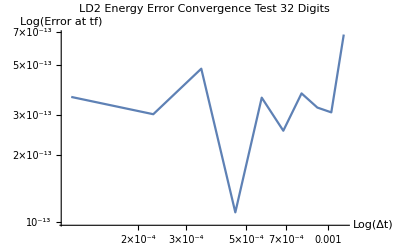

```mathematica
ListLogLogPlot[Transpose[{rs * deltax,finalerrorCN32}], Joined->True,PlotLabel->"LD2 Energy Error Convergence Test 32 Digits", AxesLabel->{"Log(Δt)","Log(Error at tf)"}]
```

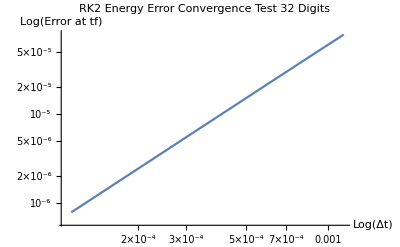

```mathematica
ListLogLogPlot[Transpose[{rs * deltax,finalerrorRK232}], Joined->True,PlotLabel->"RK2 Energy Error Convergence Test 32 Digits", AxesLabel->{"Log(Δt)","Log(Error at tf)"}]
```

```mathematica
ListLogLogPlot[Transpose[{rs * deltax,finalerrorRK432}], Joined->True,PlotLabel->"RK4 Energy Error Convergence Test Digits", AxesLabel->{"Log(Δt)","Log(Error at tf)"}]
```

-Graphics-

```mathematica
ListLogLogPlot[Transpose[{rs * deltax,finalerrorLD432}], Joined->True,PlotLabel->"LD4 Energy Error Convergence Test Digits", AxesLabel->{"Log(Δt)","Log(Error at tf)"}]
```

-Graphics-